```mathematica
DiscreteSpiral[n_Integer?Positive]:=Module[{primes,spiral,currentPos,direction,steps,stepCount},primes=Select[Range[2,n+1],PrimeQ];
spiral={0};
currentPos={0,0};
direction={{1,0},{0,1},{-1,0},{0,-1}};
steps=1;
stepCount=0;
Do[currentPos=currentPos+direction[[Mod[i,4,1]]];
spiral=Append[spiral,currentPos];
stepCount++;
If[stepCount==steps,direction=RotateLeft[direction];
If[MemberQ[primes,Length[spiral]+1],steps++;];
stepCount=0;],{i,2,n+1}];
spiral]
```

```mathematica
DiscreteSpiral[2]
```

{0,{0,1},{0,0}}

```mathematica
DiscreteSpiral[n_Integer?Positive]:=Module[{primes,spiral,currentPos,direction,steps,stepCount},primes=Select[Range[2,n+1],PrimeQ];
spiral={{0,0}};
currentPos={0,0};
direction={{1,0},{0,1},{-1,0},{0,-1}};
steps=1;
stepCount=0;
Do[currentPos=currentPos+direction[[Mod[i,4,1]]];
spiral=Append[spiral,currentPos];
stepCount++;
If[stepCount==steps,direction=RotateLeft[direction];
If[MemberQ[primes,Length[spiral]+1],steps++;];
stepCount=0;],{i,2,n+1}];
spiral]
```

```mathematica
DiscreteSpiral[2]
```

{{0,0},{0,1},{0,0}}

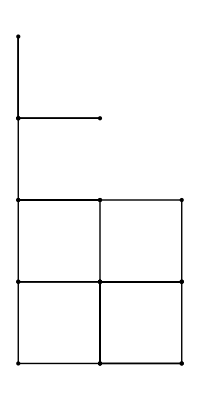

```mathematica
With[{pts=DiscreteSpiral[25]},Graphics[{Point[pts],Line[pts]}]]
```

```mathematica
DiscreteSpiral[25]
```

{{0,0},{0,1},{0,0},{1,0},{0,0},{0,-1},{1,-1},{0,-1},{0,-2},{1,-2},{0,-2},{0,-3},{1,-3},{1,-2},{1,-3},{2,-3},{2,-2},{1,-2},{2,-2},{2,-1},{1,-1},{1,-2},{2,-2},{1,-2},{1,-3},{2,-3}}

```mathematica
currentPoint={0,0};
```

```mathematica
currentPoint+={1,0}
```

{1,0}

```mathematica
currentPoint
```

{1,0}

```mathematica
currentPoint+={0,1}
```

{1,1}

```mathematica
currentPoint+={-1,0}
```

{0,1}

```mathematica
currentPoint+={}
```

```mathematica
Differences[{{0,0},{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1},{1,-1},{2,-1},{2,0},{2,1},{2,2},{1,2},{0,2},{-1,2},{-2,2},{-2,1},{-2,0},{-2,-1},{-2,-2},{-1,-2},{0,-2},{1,-2},{2,-2},{3,-2}}]
```

{{1,0},{0,1},{-1,0},{-1,0},{0,-1},{0,-1},{1,0},{1,0},{1,0},{0,1},{0,1},{0,1},{-1,0},{-1,0},{-1,0},{-1,0},{0,-1},{0,-1},{0,-1},{0,-1},{1,0},{1,0},{1,0},{1,0},{1,0}}

```mathematica
First/@Differences[{{0,0},{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1},{1,-1},{2,-1},{2,0},{2,1},{2,2},{1,2},{0,2},{-1,2},{-2,2},{-2,1},{-2,0},{-2,-1},{-2,-2},{-1,-2},{0,-2},{1,-2},{2,-2},{3,-2}}]
```

{1,0,-1,-1,0,0,1,1,1,0,0,0,-1,-1,-1,-1,0,0,0,0,1,1,1,1,1}

```mathematica
Catenate[ConstantArray[#,2]&/@{-1,0,1}]
```

{-1,-1,0,0,1,1}

```mathematica
Table[{Array[1&,n],Array[0&,n]},{n,1,5}]//Flatten
```

{1,0,1,1,0,0,1,1,1,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,1,0,0,0,0,0}